```mathematica
Format[mu]:=μ;Format[xi]:=ξ;
Format[ga]:=ga;Format[ga1]:=Subscript[γ,1];Format[ga2]:=Subscript[γ,2];
Format[μ1]:=Subscript[μ,1];Format[μ2]:=Subscript[μ,2];
Format[α1]:=Subscript[α,1];Format[α2]:=Subscript[α,2];Format[μ3]:=Subscript[μ,3];Format[μ0]:=Subscript[μ,0];
Format[th]:=θ;
Format[La]:=Λ;Format[β1]:=Subscript[β,1];Format[β2]:=Subscript[β,2];
Format[i1]:=Subscript[i,1];Format[i2]:=Subscript[i,2];
Format[i12]:=Subscript[i,12];
```

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];
<<EpidCRN`;
?EpidCRN`*
```

Load CRNT

```mathematica
(*Two-Strain Coinfection Model with Logistic Growth*)
RN={0->"s","s"+"i1"->2*"i1","s"+"i2"->2*"i2","i1"+"i2"->"i2"+"i12","i1"+"i2"->"i1"+"i12","i1"+"i12"->2*"i12","i2"+"i12"->2*"i12","s"+"i12"->"i1"+"i12","s"+"i12"->"i2"+"i12","s"+"i12"->2*"i12","s"->0,"i1"->0,"i2"->0,"i12"->0};

rts={b,α1*s*i1,α2*s*i2,γ1*i1*i2,γ2*i1*i2,η1*i1*i12,η2*i2*i12,β1*s*i12,β2*s*i12,α3*s*i12,μ0*s,μ1*i1,μ2*i2,μ3*i12};
(*rts=rtMass*{1,1/(1+a1*i1),1/(1+a2*i2),1,1,1};*)
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
cOm={β1->0,β2->0,γ1->0,γ2->0,b->r*s*(1-s/K)};cb=b->r*s*(1-s/K);
(*test extMat*)
{spe, al, be, gamma, Rv, RHS, {defFormula, defTerms, defResult}}= extMat[RN]; 
gamma//MatrixForm;gamma//MatrixForm
minSiph[spe,asoRea[RN]]
{RHS,var,par,cp,mSi,Jx,Jy,E0,ngm,R0A,EA,E1t,E2t}=bdCo[RN, rts];
Print["R0A=",R0A," E0=",E0,"EA length is ",EA//Length," ngm=",ngm//MatrixForm," eigs are",ngm//Eigenvalues]

Print["R1,R2,... are",R0A/.E0," E1t,
E2t="]
E1t
E2t
in1=2;in2=2;
Print["After examining E1t,E2t, R12,R21 are",R12=R0A[[1]]/.E2t[[in2]],"  ", R21=R0A[[3]]/.E1t[[in1]]]
{E1,E2,R12,R21,coP}=invNr[E1t,E2t,R0A,E0,par,cp,in1,in2];
```

reactions and transitions: (0→s | b
i1+s→2 i1 | i1 s α1
i2+s→2 i2 | i2 s α2
i1+i2→i12+i2 | i1 i2 γ1
i1+i2→i1+i12 | i1 i2 γ2
i1+i12→2 i12 | i1 i12 η1
i12+i2→2 i12 | i12 i2 η2
i12+s→i1+i12 | i12 s β1
i12+s→i12+i2 | i12 s β2
i12+s→2 i12 | i12 s α3
s→0 | s μ0
i1→0 | i1 μ1
i2→0 | i2 μ2
i12→0 | i12 μ3)

(1 | -1 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | 0 | 0
0 | 1 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | -1)

{{i1,i12},{i2,i12}}

R0A={(s α1)/μ1,(s α3)/μ3,(s α2)/μ2} E0={s→b/μ0,i1→0,i2→0,i12→0}EA length is 2 ngm=((s α1)/μ1 | 0 | (s β1)/μ3
0 | (s α2)/μ2 | (s β2)/μ3
0 | 0 | (s α3)/μ3) eigs are{(s α3)/μ3,(s α2)/μ2,(s α1)/μ1}

R1,R2,... are{(b α1)/(μ0 μ1),(b α3)/(μ0 μ3),(b α2)/(μ0 μ2)} E1t,
E2t=

{{i1→0,s→b/μ0},{i1→(b α1-μ0 μ1)/(α1 μ1),s→μ1/α1}}

{{i2→0,s→b/μ0},{i2→(b α2-μ0 μ2)/(α2 μ2),s→μ2/α2}}

After examining E1t,E2t, R12,R21 are(α1 μ2)/(α2 μ1)  (α2 μ1)/(α1 μ2)

Selected E1 (solution 2): {i1→(b α1-μ0 μ1)/(α1 μ1),s→μ1/α1}

Selected E2 (solution 2): {i2→(b α2-μ0 μ2)/(α2 μ2),s→μ2/α2}

invasion numbers are{(α3 μ1)/(α1 μ3),(α1 μ2)/(α2 μ1)}

under coP: {} invasion nrs are{(α3 μ1)/(α1 μ3),(α1 μ2)/(α2 μ1)} repr nrs are{(b α1)/(μ0 μ1),(b α3)/(μ0 μ3)}

END invNr OUTPUT

```mathematica
eq=Thread[RHS==0];RHSO=RHS/.cOm;parO=Par[RHSO,var];
(*ct=Join[Thread[var>=0],Thread[parO>0]];*)
eqO=Join[eq/.cOm,Thread[parO>0]];so=Solve[(eq/.cOm),var];
(*assumptions and equations*)eq=Thread[RHS==0];
RHSO=RHS/. cOm;
parO=Par[RHSO,var];cpO=Thread[parO>0];
parAss=And@@cpO;
(*solve*)
so=Solve[eq/. cOm,var];(*10 solutions*)
       keepQ[sol_]:=Reduce[parAss&&And@@Thread[(var/. sol)>=0],par,Reals]=!=False;
so8=Select[so,keepQ];  
allZeroQ[sol_]:=And@@((#/. sol)===0&/@var);

so7=DeleteCases[so8,_?(allZeroQ)];   (*drop {s->0,i1->0,i2->0,i12->0}*)
so7v=remZ/@(var/.so7//Factor);wh=whenP/@so7v//FullSimplify;
Print[so7v//Length," sols ", so7]
Print[" with pos cnds"]
ClearAll[rmL];
SetAttributes[rmL,HoldFirst];

rmL[pat_]:=Function[{expr},Module[{p=HoldPattern[pat],parts},If[Head[expr]===And,parts=DeleteCases[List@@Unevaluated[expr],p];
Switch[Length@parts,0,True,1,First@parts,_,And@@parts],If[MatchQ[expr,p],True,expr]]],HoldAll];

(*examples*)
whS=rmL[μ0<r]/@wh
```

7 sols {{s→(K (r-μ0))/r,i1→0,i2→0,i12→0},{s→μ3/α3,i1→0,i2→0,i12→-(-K r α3+K α3 μ0+r μ3)/(K α3^2)},{s→-(-K r η2+K η2 μ0-K α3 μ2+K α2 μ3)/(r η2),i1→0,i2→-(K r α3 η2-K α3 η2 μ0+K α3^2 μ2-K α2 α3 μ3-r η2 μ3)/(r η2^2),i12→-(-K r α2 η2+K α2 η2 μ0-K α2 α3 μ2+r η2 μ2+K α2^2 μ3)/(r η2^2)},{s→μ2/α2,i1→0,i2→-(-K r α2+K α2 μ0+r μ2)/(K α2^2),i12→0},{s→μ1/α1,i1→-(-K r α1+K α1 μ0+r μ1)/(K α1^2),i2→0,i12→0},{s→-(-K r η1+K η1 μ0-K α3 μ1+K α1 μ3)/(r η1),i1→-(K r α3 η1-K α3 η1 μ0+K α3^2 μ1-K α1 α3 μ3-r η1 μ3)/(r η1^2),i2→0,i12→-(-K r α1 η1+K α1 η1 μ0-K α1 α3 μ1+r η1 μ1+K α1^2 μ3)/(r η1^2)},{s→-(η2 μ1-η1 μ2)/(α2 η1-α1 η2),i1→-1/(K (α2 η1-α1 η2)^2)(K r α2 η1 η2-K r α1 η2^2-K α2 η1 η2 μ0+K α1 η2^2 μ0+r η2^2 μ1+K α2 α3 η1 μ2-K α1 α3 η2 μ2-r η1 η2 μ2-K α2^2 η1 μ3+K α1 α2 η2 μ3),i2→-1/(K (α2 η1-α1 η2)^2)(-K r α2 η1^2+K r α1 η1 η2+K α2 η1^2 μ0-K α1 η1 η2 μ0-K α2 α3 η1 μ1+K α1 α3 η2 μ1-r η1 η2 μ1+r η1^2 μ2+K α1 α2 η1 μ3-K α1^2 η2 μ3),i12→-(-α2 μ1+α1 μ2)/(-α2 η1+α1 η2)}}

with pos cnds

{True,K α3 μ0+r μ3<K r α3,K α2 μ0+r μ2<K r α2&&(K α3 (r η2-η2 μ0+α3 μ2))/(K α2 α3+r η2)<μ3<(-r η2 μ2+K α2 (r η2-η2 μ0+α3 μ2))/(K α2^2),K α2 μ0+r μ2<K r α2,K α1 μ0+r μ1<K r α1,K α1 μ0+r μ1<K r α1&&(K α3 (r η1-η1 μ0+α3 μ1))/(K α1 α3+r η1)<μ3<(-r η1 μ1+K α1 (r η1-η1 μ0+α3 μ1))/(K α1^2),(α1 η2<α2 η1&&μ0<r&&K α1 μ0+r μ1<K r α1&&(α2 μ1)/α1<μ2<(K (α2 η1-α1 η2) (r-μ0)+K α2 α3 μ1+r η2 μ1)/(K α1 α3+r η1)&&(α3 μ2+η2 (r-μ0+(r η2 μ1-r η1 μ2)/(K α2 η1-K α1 η2)))/α2<μ3<(-K (α2 η1-α1 η2) (r η1-η1 μ0+α3 μ1)+r η1 (-η2 μ1+η1 μ2))/(K α1 (-α2 η1+α1 η2)))||(α1 η2>α2 η1&&μ0<r&&(-K (α2 η1-α1 η2) (r η1-η1 μ0+α3 μ1)+r η1 (-η2 μ1+η1 μ2))/(K α1 (-α2 η1+α1 η2))<μ3<(α3 μ2+η2 (r-μ0+(r η2 μ1-r η1 μ2)/(K α2 η1-K α1 η2)))/α2&&α1 μ2<α2 μ1&&((K α1 μ0+r μ1<K r α1&&r η2 μ1+K (r α2 η1+α1 η2 μ0+α2 α3 μ1)<r η1 μ2+K (r α1 η2+α2 η1 μ0+α1 α3 μ2))||(K (α2 η1-α1 η2) (r-μ0))/(K α2 α3+r η2)+μ1≤0))}

```mathematica
wh7=whS[[7]][[1]]//FullSimplify
```

α1 η2<α2 η1&&μ0<r&&K α1 μ0+r μ1<K r α1&&(α2 μ1)/α1<μ2<(K (α2 η1-α1 η2) (r-μ0)+K α2 α3 μ1+r η2 μ1)/(K α1 α3+r η1)&&(α3 μ2+η2 (r-μ0+(r η2 μ1-r η1 μ2)/(K α2 η1-K α1 η2)))/α2<μ3<(-K (α2 η1-α1 η2) (r η1-η1 μ0+α3 μ1)+r η1 (-η2 μ1+η1 μ2))/(K α1 (-α2 η1+α1 η2))

```mathematica
wh7//Length
```

2

```mathematica
wh2=DeleteElements[wh,{2,3}];
wh2//Length
wh2
```

5

{μ2<K α2&&(K α3 (r η2+α3 μ2))/(K α2 α3+r η2)<μ3<(K r α2 η2+K α2 α3 μ2-r η2 μ2)/(K α2^2),μ2<K α2,μ1<K α1,μ1<K α1&&(K α3 (r η1+α3 μ1))/(K α1 α3+r η1)<μ3<(K r α1 η1+K α1 α3 μ1-r η1 μ1)/(K α1^2),(α1 η2<α2 η1&&μ1<K α1&&(α2 μ1)/α1<μ2<(K r α2 η1-K r α1 η2+K α2 α3 μ1+r η2 μ1)/(K α1 α3+r η1)&&(r η2+α3 μ2+(r η2 (η2 μ1-η1 μ2))/(K (α2 η1-α1 η2)))/α2<μ3<(-K (α2 η1-α1 η2) (r η1+α3 μ1)+r η1 (-η2 μ1+η1 μ2))/(K α1 (-α2 η1+α1 η2)))||(α1 η2>α2 η1&&(-K (α2 η1-α1 η2) (r η1+α3 μ1)+r η1 (-η2 μ1+η1 μ2))/(K α1 (-α2 η1+α1 η2))<μ3<(r η2+α3 μ2+(r η2 (η2 μ1-η1 μ2))/(K (α2 η1-α1 η2)))/α2&&α1 μ2<α2 μ1&&((K α1>μ1&&K r α1 η2+K α1 α3 μ2+r η1 μ2>K r α2 η1+K α2 α3 μ1+r η2 μ1)||K r α1 η2≥K r α2 η1+K α2 α3 μ1+r η2 μ1))}

```mathematica
wh2[[1]]
```

μ2<K α2&&(K α3 (r η2+α3 μ2))/(K α2 α3+r η2)<μ3<(K r α2 η2+K α2 α3 μ2-r η2 μ2)/(K α2^2)

```mathematica
reCL[whenP[so7v[[2]]]]
```

```mathematica
reCL[Reduce[parAss&&Thread[#>0],parO],cpO]&;
posC[so7v[[2]]]

posC/@so7v
```

7

{{K},{μ3/α3,(r (K α3-μ3))/(K α3^2)},{(K (r η2+α3 μ2-α2 μ3))/(r η2),-(K r α3 η2+K α3^2 μ2-K α2 α3 μ3-r η2 μ3)/(r η2^2),(K r α2 η2+K α2 α3 μ2-r η2 μ2-K α2^2 μ3)/(r η2^2)},{μ2/α2,(r (K α2-μ2))/(K α2^2)},{μ1/α1,(r (K α1-μ1))/(K α1^2)},{(K (r η1+α3 μ1-α1 μ3))/(r η1),-(K r α3 η1+K α3^2 μ1-K α1 α3 μ3-r η1 μ3)/(r η1^2),(K r α1 η1+K α1 α3 μ1-r η1 μ1-K α1^2 μ3)/(r η1^2)},{(-η2 μ1+η1 μ2)/(α2 η1-α1 η2),(-K r α2 η1 η2+K r α1 η2^2-r η2^2 μ1-K α2 α3 η1 μ2+K α1 α3 η2 μ2+r η1 η2 μ2+K α2^2 η1 μ3-K α1 α2 η2 μ3)/(K (α2 η1-α1 η2)^2),(K r α2 η1^2-K r α1 η1 η2+K α2 α3 η1 μ1-K α1 α3 η2 μ1+r η1 η2 μ1-r η1^2 μ2-K α1 α2 η1 μ3+K α1^2 η2 μ3)/(K (α2 η1-α1 η2)^2),-(α2 μ1-α1 μ2)/(α2 η1-α1 η2)}}

Reduce::naqs: K>0&&r>0&&α1>0&&α2>0&&α3>0&&η1>0&&η2>0&&μ1>0&&μ2>0&&μ3>0&&«1» is not a quantified system of equations and inequalities.

reCL[Reduce[K>0&&r>0&&α1>0&&α2>0&&α3>0&&η1>0&&η2>0&&μ1>0&&μ2>0&&μ3>0&&{μ3/α3>0,(r (K α3-μ3))/(K α3^2)>0},{K,r,α1,α2,α3,η1,η2,μ1,μ2,μ3}],cpO]

Reduce::naqs: K>0&&r>0&&α1>0&&α2>0&&α3>0&&η1>0&&η2>0&&μ1>0&&μ2>0&&μ3>0&&«1» is not a quantified system of equations and inequalities.

General::stop: Further output of Reduce::naqs will be suppressed during this calculation.

{reCL[Reduce[K>0&&r>0&&α1>0&&α2>0&&α3>0&&η1>0&&η2>0&&μ1>0&&μ2>0&&μ3>0&&{K>0},{K,r,α1,α2,α3,η1,η2,μ1,μ2,μ3}],cpO],reCL[Reduce[K>0&&r>0&&α1>0&&α2>0&&α3>0&&η1>0&&η2>0&&μ1>0&&μ2>0&&μ3>0&&{μ3/α3>0,(r (K α3-μ3))/(K α3^2)>0},{K,r,α1,α2,α3,η1,η2,μ1,μ2,μ3}],cpO],reCL[Reduce[K>0&&r>0&&α1>0&&α2>0&&α3>0&&η1>0&&η2>0&&μ1>0&&μ2>0&&μ3>0&&{(K (r η2+α3 μ2-α2 μ3))/(r η2)>0,-(K r α3 η2+K α3^2 μ2-K α2 α3 μ3-r η2 μ3)/(r η2^2)>0,(K r α2 η2+K α2 α3 μ2-r η2 μ2-K α2^2 μ3)/(r η2^2)>0},{K,r,α1,α2,α3,η1,η2,μ1,μ2,μ3}],cpO],reCL[Reduce[K>0&&r>0&&α1>0&&α2>0&&α3>0&&η1>0&&η2>0&&μ1>0&&μ2>0&&μ3>0&&{μ2/α2>0,(r (K α2-μ2))/(K α2^2)>0},{K,r,α1,α2,α3,η1,η2,μ1,μ2,μ3}],cpO],reCL[Reduce[K>0&&r>0&&α1>0&&α2>0&&α3>0&&η1>0&&η2>0&&μ1>0&&μ2>0&&μ3>0&&{μ1/α1>0,(r (K α1-μ1))/(K α1^2)>0},{K,r,α1,α2,α3,η1,η2,μ1,μ2,μ3}],cpO],reCL[Reduce[K>0&&r>0&&α1>0&&α2>0&&α3>0&&η1>0&&η2>0&&μ1>0&&μ2>0&&μ3>0&&{(K (r η1+α3 μ1-α1 μ3))/(r η1)>0,-(K r α3 η1+K α3^2 μ1-K α1 α3 μ3-r η1 μ3)/(r η1^2)>0,(K r α1 η1+K α1 α3 μ1-r η1 μ1-K α1^2 μ3)/(r η1^2)>0},{K,r,α1,α2,α3,η1,η2,μ1,μ2,μ3}],cpO],reCL[Reduce[K>0&&r>0&&α1>0&&α2>0&&α3>0&&η1>0&&η2>0&&μ1>0&&μ2>0&&μ3>0&&{(-η2 μ1+η1 μ2)/(α2 η1-α1 η2)>0,1/(K (α2 η1-α1 η2)^2)(-K r α2 η1 η2+K r α1 η2^2-r η2^2 μ1-K α2 α3 η1 μ2+K α1 α3 η2 μ2+r η1 η2 μ2+K α2^2 η1 μ3-K α1 α2 η2 μ3)>0,1/(K (α2 η1-α1 η2)^2)(K r α2 η1^2-K r α1 η1 η2+K α2 α3 η1 μ1-K α1 α3 η2 μ1+r η1 η2 μ1-r η1^2 μ2-K α1 α2 η1 μ3+K α1^2 η2 μ3)>0,-(α2 μ1-α1 μ2)/(α2 η1-α1 η2)>0},{K,r,α1,α2,α3,η1,η2,μ1,μ2,μ3}],cpO]}

```mathematica
SetEnvironment["OPENAI_API_KEY"->"sk-proj-0nTXr29AKZZM4v3psnS1Q3TFSqreWiavN8sUvB4QpF-
hTOLmMRO2bgLsrafLRj5zNybZzLWpzYT3BlbkFJezj04dOX5t0-28A4nFVZ66cjczF-
vWQezfvj7CftJHsJIhOBi8W-T14xxlymww2z-QupYUG-oA"];ResourceFunction["AIAssistant"][]
```

ResourceFunction::usermessage: AIAssistant

Failure[…]

```mathematica
(*Get solutions*)so=Solve[eq/. cOm,var];

(*Filter for potentially positive solutions under general positive parameters*)
allZeroQ[sol_]:=And@@Thread[(var/. sol)==0];

hasObviouslyNegativeTermQ[sol_]:=Module[{values},values=var/. sol;
Or@@(MatchQ[#,-(_Symbol/_Symbol)]&/@values)  (*Only exclude obvious negatives like-μ/η*)];

soP=Select[so,!allZeroQ[#]&&!hasObviouslyNegativeTermQ[#]&];

Print["soP: ",Length[soP]," possibly positive solutions"];
```

soP: 0 possibly positive solutions

```mathematica
(*positivity conditions for survivors*)
posConds=Simplify[Thread[(var/. #)>=0],parAss]&/@soP;
res=Transpose[{soP,posConds}];


res//TableForm
```

10 sols, with 0 being nonnegative

{}

```mathematica
(*eq=Thread[(RHS/.coP)==0];
so=Solve[eq,var]//FullSimplify;
Print[so//Length," sols at nr. col coP, one is positive",so//N]*)
p0val=par/.coP;
{posSols, complexEigs, angle, eigs}=fpHopf[RHS, var, par, p0val];
angle
```

-55.5775

Auto-determined varInd: {1,2,3}

Susceptible: s

Strain 1 (first compartment): i1

Strain 2 (first compartment): i2

Computing R01=1, R02=1 intersection point...

R01-R02 intersection at: be1 = 2., be2 = 2.

Adjusted ranges: be1 ∈ [0.001, 8.], be2 ∈ [0.001, 6.]

Scanning 121 parameter combinations...

Checked 28 potential coexistence points

All Rij equations: {be1/2==1,be2/2==1,(5 be2)/(2 (3+be1))==1,(3 be1)/(2 (1+be2))==1}

DFE: 12 (10%)

E2: 33 (27%)

E1: 48 (40%)

EE-Stable: 28 (23%)

{0.765625,Null}

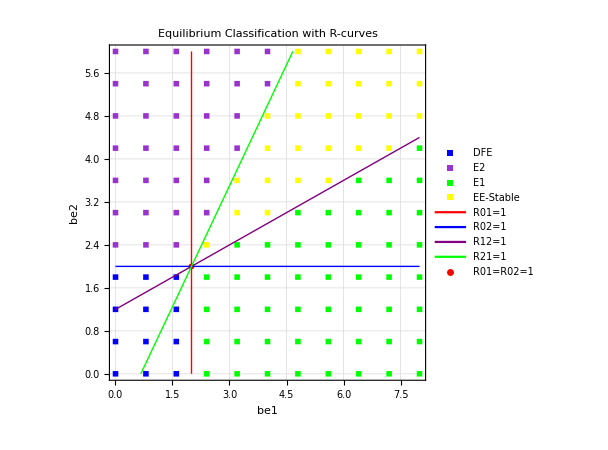

```mathematica
plotInd={3,4};
steTol=10^(-8);
staTol=10^(-10);
choTol=10^(-13);
Timing[{fPl,unC,res}=scan[RHS,var,par,coP,plotInd,mSi,Automatic,steTol,staTol,choTol,R01,R02,R12,R21];]fPl
```

```mathematica
Export["RahmanScan.pdf",fPl]
```

RahmanScan.pdf

```mathematica
scanPar[RHS, var, par, p0val, plotInd]
```

Varying parameters at indices {3,4} with center values: {4,3}

Using range mode with step size 1/20...

Total points to scan: 19200

Scanning complete!

```mathematica
Clear[scan4TS]

(*Simplified Time Series Simulation-based multiple equilibrium scanning*)
scan4TS[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,hTol_:0.01,delta_:1/20,wRan_:1,hRan_:1,R01_:Automatic,R02_:Automatic,R21_:Automatic,R12_:Automatic,tMax_:100,nInitials_:8,steadyTol_:10^(-6)]:=Block[{bifP1,bifP2,bifP1min,bifP1max,bifP2min,bifP2max,stepSize,bifP1vals,bifP2vals,totalPoints,res,outcomes,outcomeCounts,finalPlot,plotData,betterColors,useGridMode,bifParIdx1,bifParIdx2,bifP1Center,bifP2Center,progressVar,currentProgress,R01F,R02F,R21F,R12F,rCurves,coPForR,numpar,conPar,initialConditions,tsol,finalValues,I1val,I2val,tol,currentType,allSols,uniqueSols,eqType,eqTypes,steadyStateReached,lastValues,deltaCheck,icSet,ic,finalTime,pos,rhsWithParams,rhsWithFunctions,odeSystem,initialCondSystem,I1Index,I2Index,solTol},(*Define colors*)betterColors={RGBColor[0,0,1],RGBColor[0,1,0],RGBColor[0.8,0.5,0.2],RGBColor[0.6,0.3,0.8],RGBColor[1,1,0],RGBColor[1,0.5,0],RGBColor[0,0.8,0.8],RGBColor[0.8,0,0.8],RGBColor[0.5,0.8,0.5],RGBColor[0.8,0.8,0.5],RGBColor[1.0,0.0,1.0]};
(*Find indices of I1 and I2 in var*)I1Index=Position[var,I1][[1,1]];
I2Index=Position[var,I2][[1,1]];
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Extract bifurcation parameter indices*)bifParIdx1=First[plotInd];
bifParIdx2=Last[plotInd];
bifP1Center=Part[p0val,bifParIdx1];
bifP2Center=Part[p0val,bifParIdx2];
If[useGridMode,(*GRID MODE*)bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1min+(bifP1max-bifP1min)*k/(gridRes-1),{k,0,gridRes-1}];
bifP2vals=Table[bifP2min+(bifP2max-bifP2min)*k/(gridRes-1),{k,0,gridRes-1}];,(*RANGE MODE*)bifP1min=Max[bifP1Center*(1-wRan),0.001];
bifP1max=bifP1Center*(1+wRan);
bifP2min=Max[bifP2Center*(1-hRan),0.001];
bifP2max=bifP2Center*(1+hRan);
bifP1vals=Table[bifP1,{bifP1,bifP1min,bifP1max,delta}];
bifP2vals=Table[bifP2,{bifP2,bifP2min,bifP2max,delta}];];
totalPoints=Length[bifP1vals]*Length[bifP2vals];
(*Initialize for time series scanning*)res={};
currentProgress=0;
progressVar=0;
tol=10^(-6);
solTol=10^(-4);
(*Create diverse initial condition sets*)initialConditions={};
(*Set 1:DFE-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 2:E1-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.001;
AppendTo[initialConditions,icSet];
(*Set 3:E2-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.001;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Set 4:EE-like*)icSet=Table[0.01/Length[var],{Length[var]}];
icSet[[I1Index]]=0.1;
icSet[[I2Index]]=0.1;
AppendTo[initialConditions,icSet];
(*Additional random initial conditions*)Do[icSet=Table[RandomReal[{0.001,0.2}],{Length[var]}];
AppendTo[initialConditions,icSet];,{nInitials-4}];
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[bifParIdx1]]=bifP1;
numpar[[bifParIdx2]]=bifP2;
conPar=Thread[par->numpar];
(*Substitute parameters in RHS*)rhsWithParams=RHS/. conPar;
rhsWithFunctions=rhsWithParams/. Thread[var->Through[var[t]]];
(*Run time series from different initial conditions*)allSols={};
Do[ic=initialConditions[[k]];
odeSystem=MapThread[#1'[t]==#2&,{var,rhsWithFunctions}];
initialCondSystem=MapThread[#1[0]==#2&,{var,ic}];
tsol=Quiet[NDSolve[Join[odeSystem,initialCondSystem],var,{t,0,tMax}]];
If[Length[tsol]>0&&tsol[[1]]=!=$Failed,finalValues=Table[var[[j]][tMax]/. tsol[[1]],{j,1,Length[var]}];
finalTime=0.9*tMax;
lastValues=Table[var[[j]][finalTime]/. tsol[[1]],{j,1,Length[var]}];
deltaCheck=Max[Abs[finalValues-lastValues]];
steadyStateReached=(deltaCheck<steadyTol);
If[steadyStateReached&&AllTrue[finalValues,#>=0&],AppendTo[allSols,finalValues]];];,{k,1,Length[initialConditions]}];
If[Length[allSols]>0,(*Find unique attractors*)uniqueSols={allSols[[1]]};
Do[If[Min[Table[Max[Abs[allSols[[i]]-uniqueSols[[j]]]],{j,1,Length[uniqueSols]}]]>solTol,AppendTo[uniqueSols,allSols[[i]]]];,{i,2,Length[allSols]}];
(*Classify equilibria*)If[Length[uniqueSols]>1,eqTypes={};
Do[{I1val,I2val}={uniqueSols[[k,I1Index]],uniqueSols[[k,I2Index]]};
eqType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];
AppendTo[eqTypes,eqType];,{k,1,Length[uniqueSols]}];
eqTypes=Sort[DeleteDuplicates[eqTypes]];
currentType=Which[ContainsAll[eqTypes,{"EE","E1"}]&&Length[eqTypes]==2,"EE-E1",ContainsAll[eqTypes,{"EE","E2"}]&&Length[eqTypes]==2,"EE-E2",ContainsAll[eqTypes,{"E1","E2"}]&&Length[eqTypes]==2,"E1-E2",True,"Multiple"];,(*Single attractor*){I1val,I2val}={uniqueSols[[1,I1Index]],uniqueSols[[1,I2Index]]};
currentType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];];
res=Append[res,{N[bifP1],N[bifP2],currentType}];,(*No solutions found*)res=Append[res,{N[bifP1],N[bifP2],"NotGAS"}];];,{bifP2,bifP2vals}];,{bifP1,bifP1vals}];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
(*Create simple plot*)plotData=Table[Select[res,#[[3]]==outcomes[[i]]&][[All,1;;2]],{i,1,Length[outcomes]}];
finalPlot=ListPlot[plotData,PlotMarkers->Table[{Style["●",betterColors[[i]]],14},{i,1,Min[Length[betterColors],Length[outcomes]]}],PlotLegends->outcomes,AspectRatio->1,PlotRange->{{bifP1min,bifP1max},{bifP2min,bifP2max}}];
(*Add original plot if provided*)If[plot=!=Automatic,finalPlot=Show[plot,finalPlot]];
(*Simple summary*)Do[Print[outcomes[[i]],": ",outcomeCounts[[i]]," (",Round[100.*outcomeCounts[[i]]/Length[res]],"%)"],{i,1,Length[outcomes]}];
(*Return NotGAS points as errors*)unClassifPoints=Select[res,#[[3]]=="NotGAS"&];
{finalPlot,unClassifPoints,res}];
```

DFE: 42 (3%)

NotGAS: 211 (17%)

E2: 341 (28%)

E1: 440 (36%)

EE: 191 (16%)

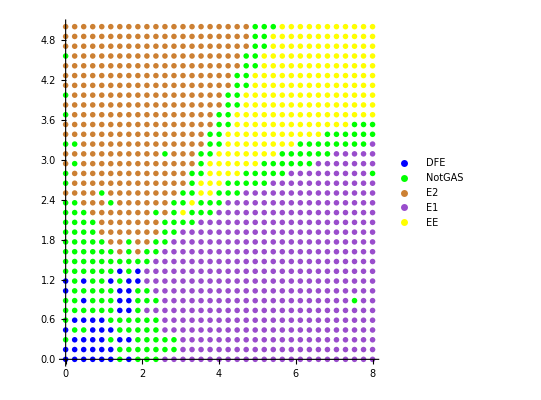

```mathematica
plotInd={1,2};
{fPl,noS,res}=scan4TS[RHS,var,par,p0val,plotInd,35,Automatic,0.01,1/20,1.0,1.0,R01,R02,R21,R12,100,8,10^(-6)];fPl
```

DFE: 48 (4%)

NotGAS: 149 (12%)

E2: 356 (29%)

E1: 453 (37%)

EE: 219 (18%)

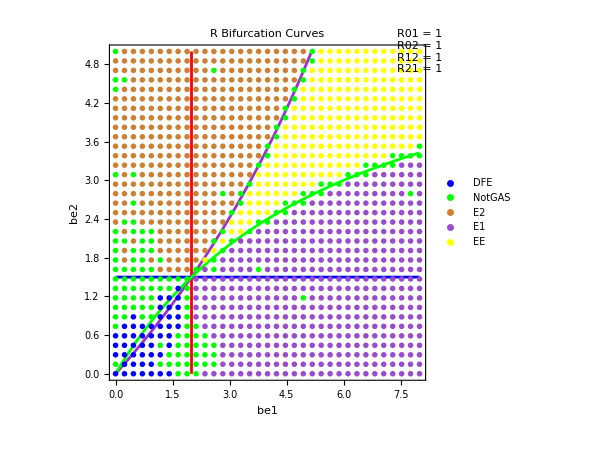

```mathematica
tMax=200;nIc=8;{fPl,noS,res}=scan4TS[RHS,var,par,p0val,plotInd,35,plot,0.01,1/20,1.0,1.0,R01,R02,R21,R12,tMax,nIc,10^(-6)];fPl
```

I1 at index 2, I2 at index 5

Varying parameters at indices {1,2} with center values: {4,5/2}

Using grid mode with 60×60 points...

Total points to scan: 3600

Initial conditions created

Scanning complete!

Found equilibrium types: {DFE (270 points),E2 (919 points),E1 (1291 points),EE (236 points),E1-E2 (344 points),error (18 points),EE-E2 (88 points),EE-E1 (213 points),Coexist (221 points)}

Including 18 errors

Summary:

DFE | 270 | 8%
E2 | 919 | 26%
E1 | 1291 | 36%
EE | 236 | 7%
E1-E2 | 344 | 10%
error | 18 | 0%
EE-E2 | 88 | 2%
EE-E1 | 213 | 6%
Coexist | 221 | 6%

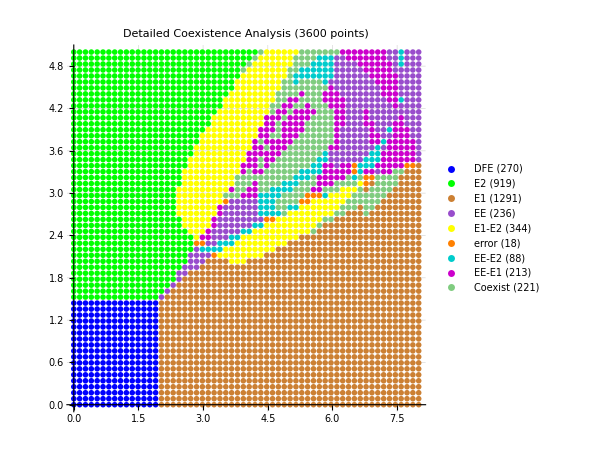

Varying be1 (center=4) and be2 (center=5/2)

Ranges: be1 ∈ {0.,8.}, be2 ∈ {0.,5.}

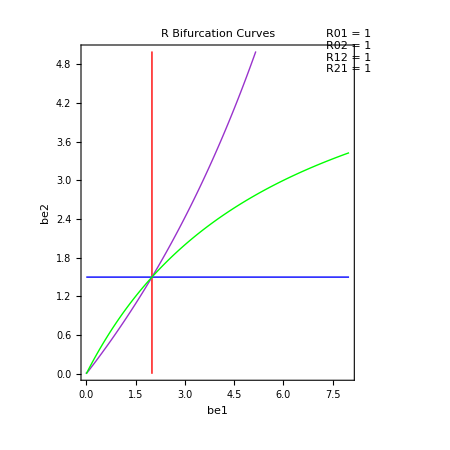

```mathematica
(*Multiple equilibrium scanning with coexistence detection*)scan4[RHS_,var_,par_,p0val_,plotInd_,gridRes_:Automatic,plot_:Automatic,hTol_:0.01,delta_:1/20,wRan_:1,hRan_:1,R01_:Automatic,R02_:Automatic,R21_:Automatic,R12_:Automatic]:=Module[{(*Parameter ranges and scanning*)β1,β2,β1min,β1max,β2min,β2max,stepSize,β1vals,β2vals,totalPoints,(*Results collection*)res,outcomes,outcomeCounts,(*Plotting and visualization*)finalPlot,plotData,betterColors,simpleTooltips,(*Mode detection*)useGridMode,β1Index,β2Index,β1Center,β2Center,(*Progress tracking*)progressVar,currentProgress,(*R curve variables*)R01F,R02F,R21F,R12F,rCurves,coPForR,(*Multiple equilibrium variables*)numpar,conPar,inP,in0,in1,in2,sol0,sol1,sol2,solMain,I1val,I2val,tol,currentType,errors,gridResults,nB1,nB2,(*Index finding*)I1Index,I2Index,solTol,allSols,uniqueSols,eqType,eqTypes},(*Define colors including detailed coexistence categories*)betterColors={RGBColor[0,0,1],(*Pure Blue for DFE*)RGBColor[0,1,0],(*Pure Green for E1*)RGBColor[0.8,0.5,0.2],(*Orange for E2*)RGBColor[0.6,0.3,0.8],(*Purple for EE*)RGBColor[1,1,0],(*Yellow for EE-E1*)RGBColor[1,0.5,0],(*Red-Orange for EE-E2*)RGBColor[0,0.8,0.8],(*Cyan for E1-E2*)RGBColor[0.8,0,0.8],(*Magenta for EE-DFE*)RGBColor[0.5,0.8,0.5],(*Light Green for E1-DFE*)RGBColor[0.8,0.8,0.5],(*Light Orange for E2-DFE*)RGBColor[1.0,0.0,1.0](*Magenta for errors/NoSol*)};
(*Find indices of I1 and I2 in var*)I1Index=Position[var,I1][[1,1]];
I2Index=Position[var,I2][[1,1]];
Print["I1 at index ",I1Index,", I2 at index ",I2Index];
(*Detect which mode we're using*)useGridMode=(gridRes=!=Automatic);
(*Extract parameter indices*)β1Index=If[Length[plotInd]>=1,plotInd[[1]],1];
β2Index=If[Length[plotInd]>=2,plotInd[[2]],2];
β1Center=p0val[[β1Index]];
β2Center=p0val[[β2Index]];
Print["Varying parameters at indices ",{β1Index,β2Index}," with center values: ",{β1Center,β2Center}];
If[useGridMode,(*GRID MODE*)Print["Using grid mode with ",gridRes,"×",gridRes," points..."];
β1min=Max[β1Center*(1-wRan),0.001];
β1max=β1Center*(1+wRan);
β2min=Max[β2Center*(1-hRan),0.001];
β2max=β2Center*(1+hRan);
β1vals=Table[β1min+(β1max-β1min)*k/(gridRes-1),{k,0,gridRes-1}];
β2vals=Table[β2min+(β2max-β2min)*k/(gridRes-1),{k,0,gridRes-1}];
stepSize="grid";,(*RANGE MODE*)Print["Using range mode with step size ",delta,"..."];
β1min=Max[β1Center*(1-wRan),0.001];
β1max=β1Center*(1+wRan);
β2min=Max[β2Center*(1-hRan),0.001];
β2max=β2Center*(1+hRan);
β1vals=Table[β1,{β1,β1min,β1max,delta}];
β2vals=Table[β2,{β2,β2min,β2max,delta}];
stepSize=delta;];
(*R curve preparation*)rCurves={};
If[R01=!=Automatic||R02=!=Automatic||R21=!=Automatic||R12=!=Automatic,coPForR=Thread[par->p0val];
coPForR=DeleteCases[coPForR,HoldPattern[par[[β1Index]]->_]|HoldPattern[par[[β2Index]]->_]];
If[R01=!=Automatic,R01F=R01/. coPForR;
AppendTo[rCurves,ContourPlot[R01F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Red,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R02=!=Automatic,R02F=R02/. coPForR;
AppendTo[rCurves,ContourPlot[R02F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Blue,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R21=!=Automatic,R21F=R21/. coPForR;
AppendTo[rCurves,ContourPlot[R21F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Green,Thick,Opacity[0.8]],PlotPoints->30]]];
If[R12=!=Automatic,R12F=R12/. coPForR;
AppendTo[rCurves,ContourPlot[R12F==1,{par[[β1Index]],β1min,β1max},{par[[β2Index]],β2min,β2max},ContourStyle->Directive[Orange,Thick,Opacity[0.8]],PlotPoints->30]]];];
totalPoints=Length[β1vals]*Length[β2vals];
Print["Total points to scan: ",totalPoints];
(*Initialize for multiple equilibrium scanning*)res={};
currentProgress=0;
progressVar=0;
tol=10^(-6);
solTol=10^(-4);(*Tolerance for comparing solutions*)(*Create initial condition arrays*)inP=Table[{var[[j]],1/Length[var]},{j,Length[var]}];(*General initial*)in0=inP;in0[[I1Index,2]]=0;in0[[I2Index,2]]=0;(*DFE:I1=I2=0*)in1=inP;in1[[I2Index,2]]=0;(*E1:I2=0*)in2=inP;in2[[I1Index,2]]=0;(*E2:I1=0*)Print["Initial conditions created"];
Print[ProgressIndicator[Dynamic[progressVar]]];
(*MAIN SCANNING LOOP WITH 4 EQUILIBRIUM SEARCHES*)Do[Do[currentProgress++;
progressVar=N[currentProgress/totalPoints];
(*Create parameter values for this grid point*)numpar=p0val;
numpar[[β1Index]]=β1;
numpar[[β2Index]]=β2;
conPar=Thread[par->numpar];
(*Four FindRoot calls with different initial conditions*)solMain=Quiet[FindRoot[RHS/. conPar,inP]];(*General*)sol0=Quiet[FindRoot[RHS/. conPar,in0]];(*DFE-like*)sol1=Quiet[FindRoot[RHS/. conPar,in1]];(*E1-like*)sol2=Quiet[FindRoot[RHS/. conPar,in2]];(*E2-like*)(*Collect all successful solutions*)allSols={};
If[Head[solMain]===List,AppendTo[allSols,var/. solMain]];
If[Head[sol0]===List,AppendTo[allSols,var/. sol0]];
If[Head[sol1]===List,AppendTo[allSols,var/. sol1]];
If[Head[sol2]===List,AppendTo[allSols,var/. sol2]];
If[Length[allSols]>0,(*Find unique solutions (within tolerance)*)uniqueSols={allSols[[1]]};
Do[If[Min[Table[Max[Abs[allSols[[i]]-uniqueSols[[j]]]],{j,1,Length[uniqueSols]}]]>solTol,AppendTo[uniqueSols,allSols[[i]]]];,{i,2,Length[allSols]}];
(*Classify based on number of unique equilibria*)If[Length[uniqueSols]>1,(*Multiple equilibria-classify each and determine coexistence type*)eqTypes={};
Do[{I1val,I2val}={uniqueSols[[k,I1Index]],uniqueSols[[k,I2Index]]};
eqType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];
AppendTo[eqTypes,eqType];,{k,1,Length[uniqueSols]}];
(*Remove duplicates and sort to get consistent naming*)eqTypes=Sort[DeleteDuplicates[eqTypes]];
(*Determine coexistence type*)currentType=Which[ContainsAll[eqTypes,{"EE","E1"}]&&Length[eqTypes]==2,"EE-E1",ContainsAll[eqTypes,{"EE","E2"}]&&Length[eqTypes]==2,"EE-E2",ContainsAll[eqTypes,{"E1","E2"}]&&Length[eqTypes]==2,"E1-E2",ContainsAll[eqTypes,{"EE","DFE"}]&&Length[eqTypes]==2,"EE-DFE",ContainsAll[eqTypes,{"E1","DFE"}]&&Length[eqTypes]==2,"E1-DFE",ContainsAll[eqTypes,{"E2","DFE"}]&&Length[eqTypes]==2,"E2-DFE",True,"Coexist" (*For 3+types or unexpected combinations*)];,(*Single equilibrium-classify by I1,I2 values*){I1val,I2val}={uniqueSols[[1,I1Index]],uniqueSols[[1,I2Index]]};
currentType=Which[I1val<tol&&I2val<tol,"DFE",I1val>=tol&&I2val<tol,"E1",I1val<tol&&I2val>=tol,"E2",True,"EE"];];
res=Append[res,{N[β1],N[β2],currentType}];,(*All FindRoot calls failed*)res=Append[res,{N[β1],N[β2],"NoSol"}];];,{β2,β2vals}];,{β1,β1vals}];
Print["Scanning complete!"];
(*Simple error detection for grid mode*)errors={};
If[useGridMode&&gridRes>2,gridResults=Table[Table[Null,{j,1,gridRes}],{i,1,gridRes}];
Do[Do[pos=Position[res,{β1vals[[i]],β2vals[[j]],_}];
If[Length[pos]>0,gridResults[[i,j]]=res[[pos[[1,1]],3]]];,{j,1,gridRes}];,{i,1,gridRes}];
Do[Do[If[gridResults[[i,j]]=!=Null,neighbors={};
If[i>1,AppendTo[neighbors,gridResults[[i-1,j]]]];
If[i<gridRes,AppendTo[neighbors,gridResults[[i+1,j]]]];
If[j>1,AppendTo[neighbors,gridResults[[i,j-1]]]];
If[j<gridRes,AppendTo[neighbors,gridResults[[i,j+1]]]];
neighbors=DeleteCases[neighbors,Null];
If[Length[neighbors]>=3&&Length[DeleteDuplicates[Join[{gridResults[[i,j]]},neighbors]]]>=4,AppendTo[errors,{β1vals[[i]],β2vals[[j]],gridResults[[i,j]]}];
pos=Position[res,{β1vals[[i]],β2vals[[j]],gridResults[[i,j]]}];
If[Length[pos]>0,res[[pos[[1,1]],3]]="error"];];];,{j,2,gridRes-1}];,{i,2,gridRes-1}];];
(*Process results*)outcomes=DeleteDuplicates[Table[res[[i,3]],{i,1,Length[res]}]];
outcomeCounts=Table[Count[res,{_,_,outcomes[[i]]}],{i,1,Length[outcomes]}];
Print["Found equilibrium types: ",Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>" points)",{i,1,Length[outcomes]}]];
Print["Including ",Length[errors]," errors"];
(*Create plot*)simpleTooltips=Table[Table[If[res[[j,3]]==outcomes[[i]],Tooltip[res[[j,1;;2]],outcomes[[i]]<>": β1="<>ToString[Round[res[[j,1]],0.01]]<>", β2="<>ToString[Round[res[[j,2]],0.01]]],Nothing],{j,1,Length[res]}],{i,1,Length[outcomes]}];
finalPlot=ListPlot[simpleTooltips,GridLines->Automatic,PlotMarkers->Table[{Style["●",betterColors[[i]]],14},{i,1,Min[Length[betterColors],Length[outcomes]]}],PlotLegends->Table[outcomes[[i]]<>" ("<>ToString[outcomeCounts[[i]]]<>")",{i,1,Length[outcomes]}],AspectRatio->1,PlotLabel->"Detailed Coexistence Analysis ("<>ToString[Length[res]]<>" points)",FrameLabel->{"Parameter "<>ToString[β1Index],"Parameter "<>ToString[β2Index]},LabelStyle->{FontSize->12,Black},ImageSize->450,PlotRange->{{β1min,β1max},{β2min,β2max}}];
(*Add R curves and overlays*)If[plot=!=Automatic,finalPlot=Show[plot,finalPlot,Sequence@@rCurves,Graphics[{EdgeForm[{Thick,Gray,Dashed}],FaceForm[None],Rectangle[{β1min,β2min},{β1max,β2max}],Blue,PointSize[0.015],Point[{{β1Center,β2Center}}]}],PlotRange->{{β1min*0.9,β1max*1.1},{β2min*0.9,β2max*1.1}}];,If[Length[rCurves]>0,finalPlot=Show[finalPlot,Sequence@@rCurves];];];
Print[Style["Summary:",FontWeight->Bold]];
Print[Grid[Table[{outcomes[[i]],outcomeCounts[[i]],ToString[Round[100.*outcomeCounts[[i]]/Length[res],1]]<>"%"},{i,1,Length[outcomes]}],Frame->All,Alignment->Left]];
{finalPlot,errors,res}];

(*Grid mode:scan4[RHS,var,par,p0val,{1,2},8,plot,0.01,1/20,1.0,1.0,R01,R02,R21,R12]*)
(*Range mode:scan4[RHS,var,par,p0val,{1,2},Automatic,plot,0.01,0.05,1.0,1.0,R01,R02,R21,R12]*)
(*Colors:DFE=Blue,E1=Green,E2=Orange,EE=Purple*)
(*Coexistence:EE-E1=Yellow,EE-E2=Red-Orange,E1-E2=Cyan,EE-DFE=Magenta,E1-DFE=Light Green,E2-DFE=Light Orange*)
{fPl,errors,res}=scan4[RHS,var,par,p0val,{1,2},60];fPl
```

Varying parameters at indices {1,2} with center values: {4,5/2}

Using grid mode with 30×30 points...

Total points to scan: 900

Scanning complete!

Found equilibrium types: {DFE (72 points),E2 (294 points),E1 (352 points),EEstable (182 points)}

Including 0 errors

Summary:

DFE | 72 | 8%
E2 | 294 | 33%
E1 | 352 | 39%
EEstable | 182 | 20%

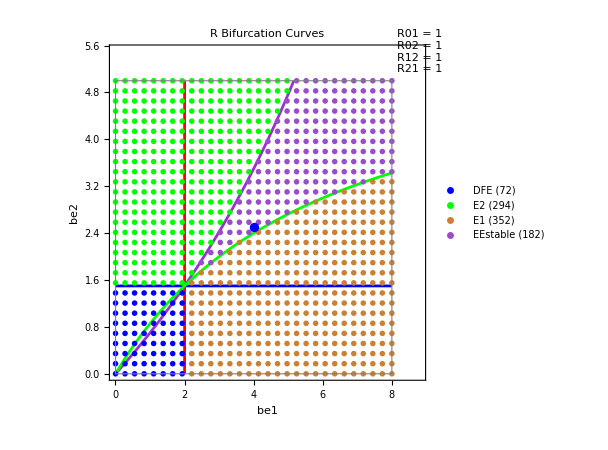

```mathematica
{plF,errors,res}=scanPar[RHS,var,par,p0val,plotInd,30,plot];plF
```

```mathematica
{plF,errors,res}=scanPar[RHS,var,par,p0val,{1,2},Automatic,plot,0.01,0.05];plot
```

Varying parameters at indices {1,2} with center values: {4,5/2}

Using range mode with step size 0.05...

Total points to scan: 16000

Scanning complete!

Found equilibrium types: {DFE (1200 points),E2 (5206 points),E1 (6379 points),EEstable (3215 points)}

Including 0 errors

Summary:

DFE | 1200 | 8%
E2 | 5206 | 33%
E1 | 6379 | 40%
EEstable | 3215 | 20%

-Graphics-